# Galáxia ESO 287-G13

## Tabelas

```mathematica
data = Import["C:\\Users\\Leoleo\\Desktop\\TCC\\Mathematica\\data_new\\287.dat"];
RC=Table[{data[[i,1]],data[[i,3]]},{i,1,26}];
Rgas=Table[{data[[i,1]],data[[i,4]]},{i,1,26}];
Erro = Table[data[[i,5]],{i,1,26}];
radii=Part[Transpose[data],1];
Vel=Part[Transpose[data],3];
err=Part[Transpose[data],5];
TableForm[data,TableHeadings->{{"ESO 287-G13"},{"Raio","","Vtotal","Vgas","Erro"}}]
```

| Raio |  | Vtotal | Vgas | Erro
ESO 287-G13 | 0.27931 | 9.14305 | 15.76 | 1.07424 | 3.87
 | 0.837931 | 8.9123 | 42.49 | 2.46665 | 4.93
 | 1.39655 | 8.75228 | 70.03 | 3.27774 | 10.44
 | 1.95517 | 8.66275 | 105.83 | 3.68792 | 4.
 | 2.51379 | 8.64403 | 118.54 | 3.84641 | 4.
 | 3.07241 | 8.69604 | 126.9 | 3.88202 | 3.08
 | 3.63103 | 8.81861 | 140.32 | 4.1325 | 4.
 | 4.18966 | 9.00001 | 144.27 | 5.44853 | 4.02
 | 4.74828 | 9.09676 | 155.65 | 7.01228 | 5.36
 | 5.3069 | 9.19495 | 149.54 | 8.38873 | 5.41
 | 5.86552 | 9.29563 | 150.65 | 9.76333 | 7.06
 | 6.42414 | 9.40034 | 155.02 | 11.1443 | 4.66
 | 6.98276 | 9.51116 | 166.94 | 12.5646 | 6.
 | 7.54138 | 9.62647 | 167.37 | 14.0251 | 2.63
 | 8.1 | 9.74586 | 163.17 | 15.4947 | 3.32
 | 8.65862 | 9.89069 | 164.38 | 16.9319 | 2.43
 | 9.21724 | 10.0609 | 160.2 | 18.5489 | 5.7
 | 9.77586 | 10.2493 | 164.47 | 20.3382 | 3.79
 | 10.3345 | 10.4562 | 172.81 | 22.3449 | 8.51
 | 10.8931 | 10.6663 | 165.95 | 24.5708 | 2.
 | 15.3621 | 11.3032 | 163.72 | 52.6146 | 10.79
 | 15.9207 | 10.7869 | 173.94 | 56.4422 | 2.
 | 18.6207 | 6.81669 | 176.44 | 67.7037 | 2.8
 | 20.6897 | 4.2309 | 182.08 | 68.486 | 2.31
 | 22.7586 | 2.37977 | 184.16 | 66.5516 | 2.07
 | 24.8276 | 1.2192 | 183.3 | 62.8426 | 2.05

## Interpolação

```mathematica
Igas = Interpolation[Rgas]
```

InterpolatingFunction[{{0.27931, 24.8276}}, <>]

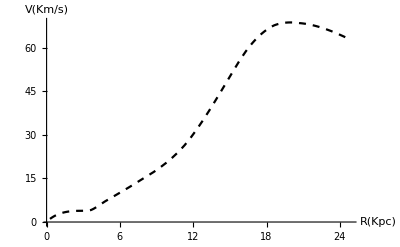

```mathematica
Gas =Plot[Igas[x],{x,0.27931,24.8276},PlotStyle->{Black,Dashed},AxesLabel->{"R(Kpc)","V(Km/s)"}]
```

## Definindo Equações

```mathematica
Vd[r_,M_]:=1/(2 Rd)(G (M *10^9) (r/Rd)^2) (BesselI[0,r/(2 Rd)] BesselK[0,r/(2 Rd)]-BesselI[1,r/(2 Rd)] BesselK[1,r/(2 Rd)]);
Vme[r_,R_,P_]:=1/r 6.4 G ((P *10^7) R^3) (1/2 Log[(r/R)^2+1]+Log[r/R+1]-ArcTan[r/R]);
G:=4.302/10^6;
Rd:=3.3;
Vt[r_,M_,R_,P_]:=Sqrt[Vd[r,M]+Vme[r,R,P]+Igas[r]^2]
```

## Ajuste

```mathematica
Ajuste= NonlinearModelFit[RC,Vt[r,M,R,P],{{R,1,50},{M,1,30},{P,4,10}},r, Weights->1/Erro^2]
```

FittedModel[√(2726.76 r^2 (BesselI[0,0.151515 r] BesselK[0,0.151515 r]-«1» «1»)+(«1»)/r+(«1»)^2)]

```mathematica
Ajuste["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
R | 28.4899 | 5.9341 | 4.80105 | 0.0000764508
M | 45.5563 | 1.26035 | 36.1458 | 9.06197×10^-22
P | 0.430196 | 0.0775027 | 5.55072 | 0.0000120272

```mathematica
a=Plot[Ajuste[x],{x,0,24},AxesOrigin->{0,0}, PlotStyle->Black];
Show[a,ListPlot[RC]];
```

InterpolatingFunction::dmval: Input value {0.000490286} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

## Gráficos

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
RCtotal = Plot[Ajuste[r],{r,0,24.82}, PlotStyle->Black, PlotRange->{{0,26},{0,183.3}}];Vstars = Plot[Sqrt[Vd[r,M]]/.M->45.56,{r,0,24.83}, PlotStyle->{Black,Dotted}];
Vhalo = Plot[Sqrt[Vme[r,R,P]]/.{R->28.48,P->0.43},{r,0,26},PlotStyle->{Black,DotDashed}];
VRC = ErrorListPlot[{Table[{RC[[i]],ErrorBar[Erro[[i]]]},{i,26}]},PlotStyle->Black,MeshStyle->PointSize[Large]];
Teste = Plot[Vt[r,M,R,P]/.{M->45.56,R->28.48,P->0.43},{r,0,24.8},PlotStyle->Black,PlotRange->{{0,26},{0,200}}];
```

InterpolatingFunction::dmval: Input value {0.000507037} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.000506629} lies outside the range of data in the interpolating function. Extrapolation will be used.

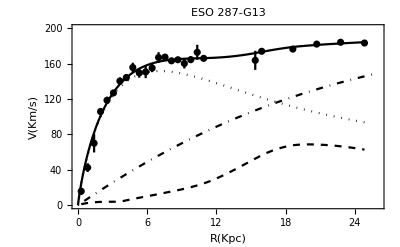

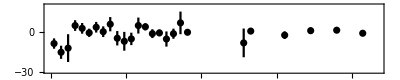

```mathematica
Show[Teste,VRC,Vstars,Vhalo,Gas, Frame->True,PlotRange->{{0,26},{0,200}},PlotLabel->"ESO 287-G13",FrameLabel->{"R(Kpc)","V(Km/s)"}]
ErrorListPlot[{Table[{Table[{data[[i,1]],Ajuste["FitResiduals"][[i]]},{i,26}][[i]],ErrorBar[Erro[[i]]]},{i,26}]}, PlotStyle->Black, MeshStyle->PointSize[Large], PlotRange->{{0,26},{-30,20}},Frame->True, AspectRatio->0.2]
```

```mathematica
chi2[M_,R_,P_]:=N[Plus@@Table[(Vel[[i]]-Vt[radii[[i]],M,P,R])^2/(err[[i]])^2,{i,Dimensions[radii][[1]]}]]
```

```mathematica
BestFit = Timing[NMinimize[{chi2[ M,P,R],M>1&&M<50&&R>.1&&R<100&&P>0.01&&P<10},{M,R,P}]]
```

{0.53125,{29.8596,{M→45.5563,R→28.4899,P→0.430195}}}